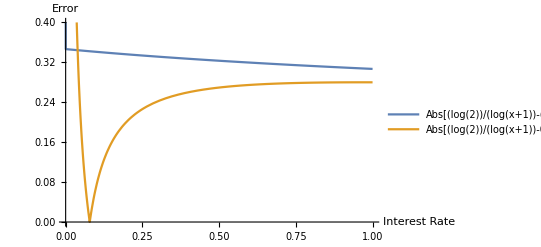

```mathematica
f[x_]:=Log[2]/Log[1+x];
g[x_]:=Log[2]/x;
h[x_]:=0.72/x;
Plot[{Abs[f[x]-g[x]],Abs[f[x]-h[x]]},{x,0,1},PlotRange->{0,0.4},AxesLabel->{"Interest Rate","Error"},PlotLegends->{y=Abs[Log[2]/Log[1+x]-Log[2]/x],y=Abs[Log[2]/Log[1+x]-0.72/x]}]
```